```mathematica
CloudDeploy[FormFunction[{"profile"->"Image"},Block[{filter,img,size},

img = #profile;
filter=-Graphics-;
(* Crop the profile to the middle square *)
size=Min[ImageDimensions[img]];
img=ImageCrop[img,{size,size}];

(* Using the min ensures highest resolution *)
size=Min[size,ImageDimensions[filter]];

(* Scale images to the same size *)
img=ColorConvert[ImageResize[img,size],"Grayscale"];
filter=ImageResize[filter,size];

ImageAdjust[Blend[{img,filter}],{.1,.1}]]&,"PNG"],Permissions->"Public"]
```

```mathematica
CloudDeploy[APIFunction[{"profile"->"Image"},Block[{filter,img,size},

img = #profile;
filter=-Graphics-;
(* Crop the profile to the middle square *)
size=Min[ImageDimensions[img]];
img=ImageCrop[img,{size,size}];

(* Using the min ensures highest resolution *)
size=Min[size,ImageDimensions[filter]];

(* Scale images to the same size *)
img=ColorConvert[ImageResize[img,size],"Grayscale"];
filter=ImageResize[filter,size];

ImageAdjust[Blend[{img,filter}],{.1,.1}]]&,"PNG"],Permissions->"Public"]
```

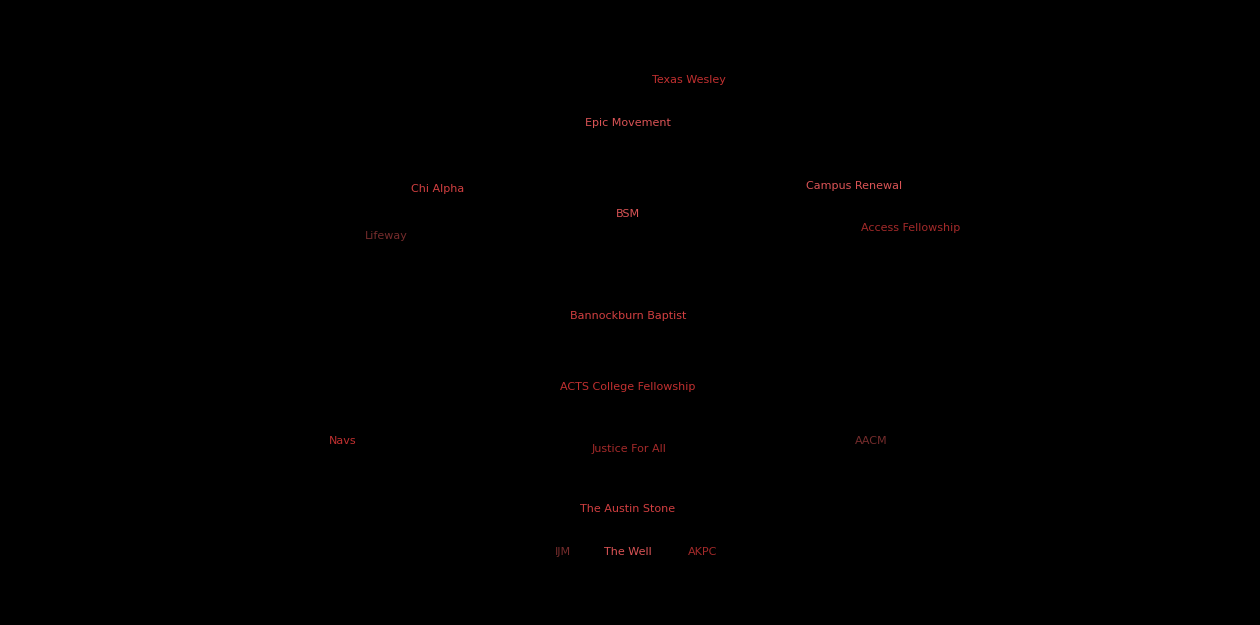

/Users/Evan/GitProjects/campusmap/RezWeekCal/wordcloud.png

```mathematica
wc=WordCloud[
{2->"AACM",2->"Texas Wesley",2->"Campus Renewal",8->"Justice For All",17->"BSM",2->"Chi Alpha",4->"Access Fellowship",7->"Epic Movement",5->"ACTS College Fellowship",1->"AKPC",16->"Bannockburn Baptist",1->"The Well",10->"Navs",8->"Lifeway",6->"The Austin Stone",1->"IJM"},
Background->Transparent,ColorFunction->Reverse[Table[ColorData["CherryTones"][i],{i,0.1,.5,0.1}]],
WordSpacings->5,
ImageSize->1260]
Export["/Users/Evan/GitProjects/campusmap/RezWeekCal/wordcloud.png",wc,"PNG"]
```